まずは、手でT->X,Mの順で固定を行う。前回、Numerical errorを起こしていた場所が特定できていたので、そこは手で落とす。
- 本当はもう少しパラメターの領域を変化させてみたかったが、計算ができなくなったので、計算できた値の周辺の解析で妥協した。

F-term ポテンシャルの計算。
このとき、vtempで計算を切り上げて、w_0を手で落とせるようにしておく。

```mathematica
ClearAll;
zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T]+μ X M+α Λ^3*Exp[-c T]/M^(1/(n-1));
W̄=W/.{T->T̄,X->X̄,M->M̄};

K=-3Log[T+T̄]+Z X*X̄+M*M̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, M]=D[W,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M]=D[K,M]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M̄]=D[K,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M M̄]=D[K,M,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T M̄]=D[K,T,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,X,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X M̄]=D[K,X,M̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M T̄]=D[K,M,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, M X̄]=D[K,M,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};
DMW=Subscript[W, M]+Subscript[K, M]*W;
OverBar[DMW]=DMW/.{T->T̄,T̄->T,X->X̄,X̄->X,M->M̄,M̄->M};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄],Subscript[K, T M̄]},{Subscript[K, X T̄],Subscript[K, X X̄],Subscript[K, X M̄]},{Subscript[K, M T̄],Subscript[K, M X̄],Subscript[K, M M̄]}};

Print["K_(I OverscriptBox[J, _])=",Kmat//MatrixForm];
Kinv=Inverse[Kmat];
Print["K^(I OverscriptBox[J, _])=",Kinv//MatrixForm];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, T M̄]=Kinv[[1,3]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];
Subscript[invK, X M̄]=Kinv[[2,3]];
Subscript[invK, M T̄]=Kinv[[3,1]];
Subscript[invK, M X̄]=Kinv[[3,2]];
Subscript[invK, M M̄]=Kinv[[3,3]];

FM=-Exp[K/2]*(Subscript[invK, M T̄]*(OverBar[DTW])+Subscript[invK, M X̄]*(OverBar[DXW])+Subscript[invK, M M̄]*(OverBar[DMW]));
FX=-Exp[K/2]*(Subscript[invK, X T̄]*(OverBar[DTW])+Subscript[invK, X X̄]*(OverBar[DXW])+Subscript[invK, X M̄]*(OverBar[DMW]));

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, T M̄]*(DTW)*(OverBar[DMW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])+Subscript[invK, X M̄]*(DXW)*(OverBar[DMW])+Subscript[invK, M T̄]*(DMW)*(OverBar[DTW])+Subscript[invK, M X̄]*(DMW)*(OverBar[DXW])+Subscript[invK, M M̄]*(DMW)*(OverBar[DMW])-3W*W̄);
(* Print["V=",vtemp]; *)


V=ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}];
```

K_(I OverscriptBox[J, _])=(3/(T+T̄)^2 | 0 | 0
0 | Z | 0
0 | 0 | 1)

K^(I OverscriptBox[J, _])=(1/3 (T+T̄)^2 | 0 | 0
0 | 1/Z | 0
0 | 0 | 1)

w_0を手でおいてしまう。そのあとに色々代入する。

```mathematica
Clear[w0];
w0=δw0;

valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

valn=2;
valΛ=10^(-3);
valC=1;
valλ=1;
valZ=1;

valμ=valλ*valΛ;
valα=valC*valΛ^(1/(valn-1));

(*Print["μ=",valμ];*)
(*Print["α=",valα];*)

(* mixing for moduli and mesons *)
valc=2Pi/50;

(* remove the dependence of the imaginary and insert parameters *)
V=Expand[V/.{ImM->0,ImX->0,ImT->0}/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ}/.{a->vala,b->valb,A->valA,B->valB,c->valc,δw0->valδw0}/.Arg->zero];
```

まずは、Tの固定から。このとき、Cosmological constantの部分はNumerical errorを起こすので、手で0にしておく。
・陳さんの修論の結果にならって、V=X^4+V_Fとして計算した。

X,Mのグラフ

-Graphics3D-

ReX→-1.36×10^-6, ReM→0.00011

V_min=-4.57054×10^6

極小値での近くのプロット

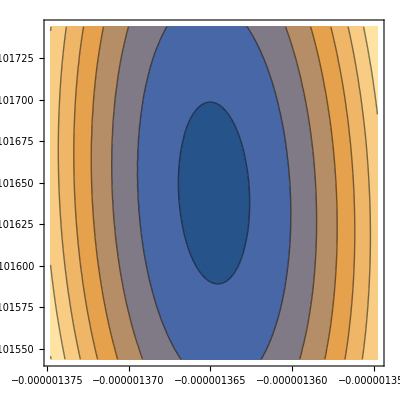

time: 1.287655

```mathematica
inittime=AbsoluteTime[];

(* 全体のスケーリング *)
sc=10^(25);

Block[{$MaxPrecision=Infinity},
(* stabilized by KL moudli potential *)
Vkl=Simplify[Expand[(ReX^4+V)*sc/.{ReT->62.40947856364392}]];
(*Print["V_kl=",Vkl];*)

Print["X,Mのグラフ"];
Print[
Plot3D[Vkl,{ReX,-1,1},{ReM,10^(-8),1},Axes->True,AxesLabel->{"X","M"}]
];

(* 極小値を見つける。(メッセージがうるさいのでQuiet) *)
Quiet[
sol=FindMinimum[Vkl,{ReX,10^(-5)},{ReM,10^(-1)},WorkingPrecision->1000,AccuracyGoal->20];
];

Print[N[sol[[2]][[1]],3],", ",N[sol[[2]][[2]],3]];

rexmid=ReX/.sol[[2]];
remmid=ReM/.sol[[2]];

Print["V_min=",Vkl/.{ReX->rexmid,ReM->remmid}];

plran=10^(-8);



Print["極小値での近くのプロット"];
(*Print[
Plot3D[Vkl,{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True,AxesLabel->{"X","M"}]
];*)

Print[
ContourPlot[Vkl,{ReX,rexmid-plran,rexmid+plran},{ReM,remmid-plran,remmid+plran},Axes->True]
];

];


Print["time: ",AbsoluteTime[]-inittime];
```

コンシステンシーチェック。F^XとかF^Mを求めておく。

```mathematica
valT=62.40947856364392;
valM=ReM/.sol[[2]];
valX=ReX/.sol[[2]];

Print["F^M=",N[FM/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}/.{ImM->0,ImX->0,ImT->0}/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ}/.{a->vala,b->valb,A->valA,B->valB,c->valc,δw0->valδw0}/.Arg->zero/.sol[[2]]/.ReT->valT,4]
];

Print["F^X=",N[FX/.{T->ReT+I ImT,T̄->ReT-I ImT,X->ReX+I ImX,X̄->ReX-I ImX,M->ReM+I ImM,M̄->ReM-I ImM}/.{ImM->0,ImX->0,ImT->0}/.{α->valα,n->valn,μ->valμ,Λ->valΛ,λ->valλ,Z->valZ}/.{a->vala,b->valb,A->valA,B->valB,c->valc,δw0->valδw0}/.Arg->zero/.sol[[2]]/.ReT->valT,4]
];
```

F^M=8.52533×10^-12

F^X=-7.88049×10^-11